```mathematica
dataA={{0,0},{4.133333333,100},{8.266666667,200},{11.33333333, 300},{17.46666667,400},{21.06666667,500},{26.26666667,600},{28.53333333,700},{32.8,800},{36.13333333,900}};

datafitA=NonlinearModelFit[dataA,{c*t+v},{c,v},t]
datafitA[{"BestFit","ParameterTable"}]
```

FittedModel[-2.44257+24.3249 t]

{-2.44257+24.3249 t, | Estimate | Standard Error | t-Statistic | P-Value
c | 24.3249 | 0.545502 | 44.5917 | 7.06166×10^-11
v | -2.44257 | 12.0113 | -0.203355 | 0.843935}

```mathematica
Needs["ErrorBarPlots`"];
dataerrA=ErrorListPlot[{{{0,0},ErrorBar[0,0]},
{{4.133333333,100},ErrorBar[0.021763983,0.2]},{{8.266666667,200},ErrorBar[0.024425885,0.4]},{{11.33333333, 300},ErrorBar[0.023526358,0.6]},{{17.46666667,400},ErrorBar[0.025751492,0.8]},{{21.06666667,500},ErrorBar[0.031954869,1]},{{26.26666667,600},ErrorBar[0.026216918,1.2]},{{28.53333333,700},ErrorBar[0.02835189,1.4]},
{{32.8,800},ErrorBar[0.030974758,1.6]},
{{36.3333333,900},ErrorBar[0.025594469,1.8]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
pplotA=ListPlot[dataA ,PlotStyle->{Black,Thickness[0.003]},PlotLegends-> {"Datos experimentales"}];

graphA=Plot[datafitA[t],{t,-1,40},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{-1,40},{-20,1000}},Frame->True,FrameLabel->{Style["Δt / ns",Bold,16],Style["Δd / cm",16,Bold]},PlotLegends->{"Curva de retraso temporal"}];
```

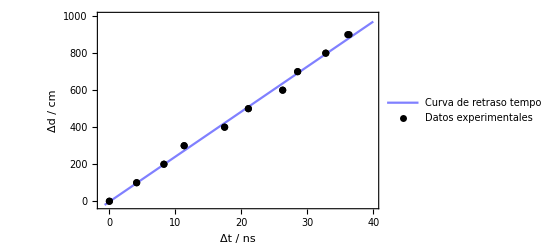

```mathematica
Show[graphA,pplotA,dataerrA]
```

```mathematica
dataD={{0,0},{1.066666667,100},{-0.4,200},{3.6, 300},{3.6,400},{-32.133333337,500},{-45.6,600},{-19.06666667,700},{-46.13333333,800},{-43.73333333,900}};

datafitD=NonlinearModelFit[dataD,{c*t+v},{c,v},t]
datafitD[{"BestFit","ParameterTable"}]
```

FittedModel[244.185-11.5109 t]

{244.185-11.5109 t, | Estimate | Standard Error | t-Statistic | P-Value
c | -11.5109 | 2.67635 | -4.30097 | 0.00261233
v | 244.185 | 73.5073 | 3.32192 | 0.01051}

```mathematica
Needs["ErrorBarPlots`"];
dataerrD=ErrorListPlot[{{{0,0},ErrorBar[0,0]},
{{1.066666667,100},ErrorBar[0.033343914,0.2]},{{-0.4,200},ErrorBar[0.025868633,0.4]},
{{3.6, 300},ErrorBar[0.027566087,0.6]},
{{3.6,400},ErrorBar[0.047914428,0.8]},{{-32.133333337,500},ErrorBar[0.192076872,1]},{{-45.6,600},ErrorBar[0.096745739,1.2]},{{-19.06666667,700},ErrorBar[0.098525281,1.4]},
{{-46.13333333,800},ErrorBar[0.050471199,1.6]},
{{-43.73333333,900},ErrorBar[0.105900499,1.8]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
pplotD=ListPlot[dataD ,PlotStyle->{Black,Thickness[0.003]},PlotLegends-> {"Datos experimentales"}];

graphD=Plot[datafitD[t],{t,-50,5},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{-50,5},{-15,910}},Frame->True,FrameLabel->{Style["Δt / ns",Bold,16],Style["Δd / cm",16,Bold]},PlotLegends->{"Curva de retraso temporal"}];
```

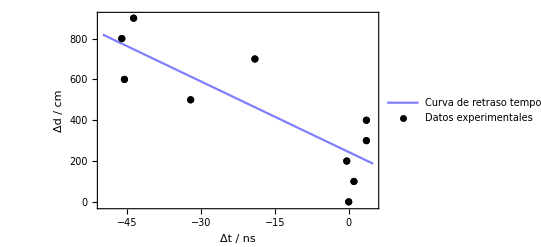

```mathematica
Show[graphD,pplotD,dataerrD]
```